```mathematica
(********************* PARAMETERS *********************)
logabounds={{-5,5}};
logbbounds={{-5,5}};
Npoints={100,200};
logab=Flatten[Outer[List,Range[-20,20,0.1],Range[-20,20,0.1]],1];
logabzoom=Flatten[Outer[List,Range[-5,5,0.05],Range[-5,5,0.05]],1];
(********************* NONDIMENSIONALIZED RATE OF mRNA PRODUCTION r̂(x)=(r(xX0)-r(0))/(r(∞)-r(0))=(a x + x.b2)/(1 + b x + x.b2); x=X/X0*********************)
(********************* r(X) =r̂(X/X0)(r(∞)-r(0))+r(0) *********************)
rhat[a_,b_,x_]:=(a* x + x^2)/(1 + b* x + x ^2)
(********************* NORMALIZED RATE OF mRNA PRODUCTION r̃(X)= (r(X)-rmin)/(rmax-rmin)=r̂(x)=(r̂(X/X0)(r(∞)-r(0)))/((r̂ max-r̂ min)(r(∞)-r(0))) +(r(0)-r̂ min(r(∞)-r(0))-r(0))/((r̂ max-r̂ min)(r(∞)-r(0)))
                                                                       = (r̂(X/X0)-r̂ min)/(r̂ max-r̂ min)    *********************)

(********************* COMPUTATION of (d r̂)/dlnx(x) : drhat(X) *********************)
rhatlnx[a_,b_,lnx_]:=(a* Exp[lnx] +  Exp[lnx] ^2)/(1 + b*  Exp[lnx]  +  Exp[lnx]  ^2)
drhatofX=FullSimplify[D[rhatlnx[a,b,lnx],{lnx,1}]/.lnx->Log[x]];
drhat[a_,b_,x_]:=Evaluate[(drhatofX /.{ x->x, a->a, b->b})];
Xextremum=Solve[drhat[a,b,x]==0&&x>0&&b>0,x,Reals];
XextremumForDoublyInflectedCurves[a_,b_]:=1/(a-b)+√((1+a^2-a b)/(a-b)^2)
RextremumForDoublyInflectedCurves[a_,b_]:=rhat[a,b,XextremumForDoublyInflectedCurves[a,b]]
(*We are interested in the slope of r̃(X) with respect to ln(X)*)

(********************* COMPUTATION of |(d r̃)/dlnX(X)| = |(d r̂)/dlnX(X)1/(r̂ max-r̂ min)| : drtilde(X) *********************)
drtilde[a_,b_,x_]:=
If[(a<0&&0≤b),
	Abs[drhat[a,b,x]/(RextremumForDoublyInflectedCurves[a,b]-1)],
	If[(a>0&&0≤b<a),
		Abs[drhat[a,b,x]/RextremumForDoublyInflectedCurves[a,b]],
Abs[drhat[a,b,x]]]]
```

```mathematica
(********************* COMPUTATION of (d.b2 r̂)/(dlnx.b2)(x) : d2rhat(X) *********************)
(*The number of inflections of a curve r̂ is the same than the curve  r̃, or r because they only differ by addition and mutliplication of constants*)
(*Therefore, we compute the number 2nd derivative with respect to ln(x) of r and count its zeros*)
d2rhatofX=FullSimplify[D[rhatlnx[a,b,lnx],{lnx,2}]/.lnx->Log[x]];
d2rhat[a_,b_,x_]:=Evaluate[(d2rhatofX /.{ x->x, a->a, b->b})];
```

```mathematica
Xinf=Solve[d2rhat[a,b,x]==0&&x>0&&b>0,x,Reals];
```

```mathematica
(********************* CONDITIONS FOR HAVING 1, 2 or 3 INFLECTIONS - dervied in EqS98toS100.nb *********************)
```

```mathematica
Inflection1[a_,b_]:=(0<a<2&&a<b<Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,1])||(2<a<Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753&&(a<b<Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,1]||Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,2]<b<Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,3]))||(a>Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753&&a<b<Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,1])
```

```mathematica
Inflection2[a_,b_]:=(a<0&&0≤b)||(a>0&&0≤b<a)
```

```mathematica
Inflection3[a_,b_]:=b≥0&&(((0<a<2||(a>2&&a<Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753&&b<Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,2])||a>Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753)&&b>Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,1])||(a<Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753&&a>2&&b>Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,3]))
```

```mathematica
(********************* VALUE OF X AT ith INFLECTION *********************)
```

```mathematica
Xinflection[a_,b_,i_]:=Root[a+(4-a b) #1+(-6 a+3 b) #1^2+(-4-a b+b^2) #1^3+(a-b) #1^4&,i]
```

```mathematica
(********************* VALUE OF THE NORMALIZED SLOPE AT ith INFLECTION *********************)
```

```mathematica
Slope[a_,b_,i_]:=drtilde[a,b,Xinflection[a,b,i]]
(********************* VALUES OF SLOPE AT FIRST INFLECTION *********************)
```

```mathematica
(*If the curve has 3 inflections the first inflection occurs at Xinflection[a,b,2].
If the curve has 1 inflection (or is equilibrium like) the first inflection ocuurs at Xinflection[a,b,2] or Xinflection[a,b,4].
So all the monotonic curves have their first inflection point either at Xinflection[a,b,2] or Xinflection[a,b,4].
If the curve has two inflections (or is nonmonotonic) the first inflection occurs at Xinflection[a,b,1] or Xinflection[a,b,3].*)
```

```mathematica
SlopeAtInflectionForSinglyInflectedCurves[a_,b_]:=
If[Element[Xinflection[a,b,2],PositiveReals],
         Slope[a,b,2],
         If[Element[Xinflection[a,b,4],PositiveReals],
             Slope[a,b,4]]]

SlopeAtFristInflectionForDoublyInflectedCurves[a_,b_]:=
If[Element[Xinflection[a,b,1],PositiveReals],
        Slope[a,b,1],
         If[Element[Xinflection[a,b,3],PositiveReals],
               Slope[a,b,3]]]

SlopeAtFirstInflectionForTriplyInflectedCurves[a_,b_]:=
Slope[a,b,2]
```

```mathematica
SlopeFirstInflection[a_,b_]:=
If[Inflection3[a,b],
	SlopeAtFirstInflectionForTriplyInflectedCurves[a,b],
	If[Inflection2[a,b],
		SlopeAtFristInflectionForDoublyInflectedCurves[a,b],
SlopeAtInflectionForSinglyInflectedCurves[a,b]]]
```

```mathematica
(********************* PLOTS OF SLOPE AT FIRST INFLECTION *********************)
```

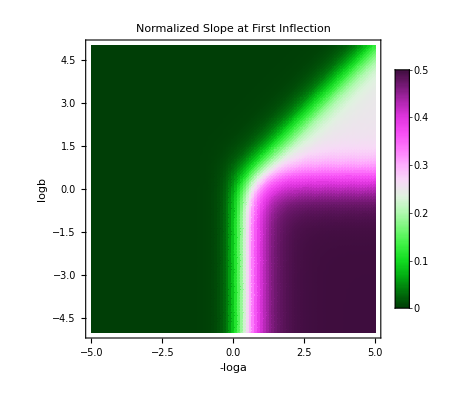

```mathematica
PlotFirstInflectionNegativea=Quiet[DensityPlot[{SlopeFirstInflection[-10^loga,10^logb]},{loga,logabounds[[1]][[1]],logabounds[[1]][[2]]},{logb,logbbounds[[1]][[1]],logbbounds[[1]][[2]]},PlotPoints->{Npoints[[1]],Npoints[[1]]},ColorFunction->"GreenPinkTones",FrameLabel->{"-loga","logb"},PlotLegends->Automatic,PlotLabel->"Normalized Slope at First Inflection",PlotRange->{Full,Full,Full}]]
```

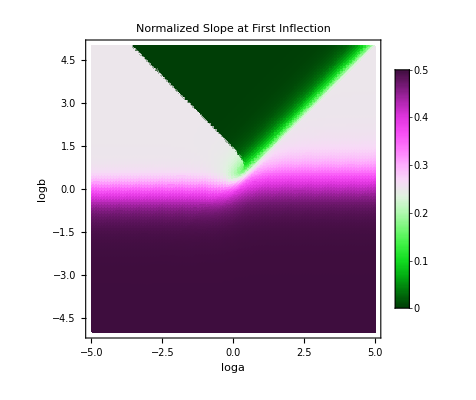

```mathematica
PlotFirstInflectionPositivea=Quiet[DensityPlot[{SlopeFirstInflection[10^loga,10^logb]},{loga,logabounds[[1]][[1]],logabounds[[1]][[2]]},{logb,logbbounds[[1]][[1]],logbbounds[[1]][[2]]},PlotPoints->{Npoints[[1]],Npoints[[1]]},ColorFunction->"GreenPinkTones",FrameLabel->{"loga","logb"},PlotLegends->Automatic,PlotLabel->"Normalized Slope at First Inflection",PlotRange->{Full,Full,Full}]]
```

```mathematica
(********************* VALUES OF SLOPE AT LAST INFLECTION *********************)
```

```mathematica
(*If the curve has 3 inflections the third inflection occurs at Xinflection[a,b,4].
If the curve has 2 inflections (or is nonmonotonic) the second inflection occurs Xinflection[a,b,2] or Xinflection[a,b,4]*)
```

```mathematica
SlopeAtLastInflectionForDoublyInflectedCurves[a_,b_]:=
If[Element[Xinflection[a,b,2],PositiveReals],
         Slope[a,b,2],
         If[Element[Xinflection[a,b,4],PositiveReals],
               Slope[a,b,4]]]
SlopeAtLastInflectionForTriplyInflectedCurves[a_,b_]:=
Slope[a,b,4]
```

```mathematica
SlopeLastInflection[a_,b_]:=
If[Inflection3[a,b],
	SlopeAtLastInflectionForTriplyInflectedCurves[a,b],
	If[Inflection2[a,b],
		SlopeAtLastInflectionForDoublyInflectedCurves[a,b],
SlopeAtInflectionForSinglyInflectedCurves[a,b]]]
```

```mathematica
(********************* PLOTS OF SLOPE AT LAST INFLECTION *********************)
```

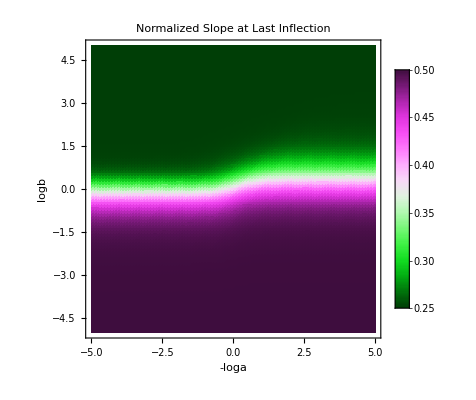

```mathematica
PlotLastInflectionNegativea=Quiet[DensityPlot[{SlopeLastInflection[-10^loga,10^logb]},{loga,logabounds[[1]][[1]],logabounds[[1]][[2]]},{logb,logbbounds[[1]][[1]],logbbounds[[1]][[2]]},PlotPoints->{Npoints[[1]],Npoints[[1]]},ColorFunction->"GreenPinkTones",FrameLabel->{"-loga","logb"},PlotLegends->Automatic,PlotLabel->"Normalized Slope at Last Inflection",PlotRange->{Full,Full,Full}]]
```

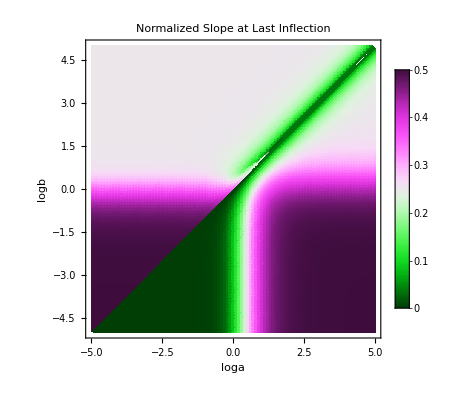

```mathematica
PlotLastInflectionPositivea=Quiet[DensityPlot[{SlopeLastInflection[10^loga,10^logb]},{loga,logabounds[[1]][[1]],logabounds[[1]][[2]]},{logb,logbbounds[[1]][[1]],logbbounds[[1]][[2]]},PlotPoints->{Npoints[[1]],Npoints[[1]]},ColorFunction->"GreenPinkTones",FrameLabel->{"loga","logb"},PlotLegends->Automatic,PlotLabel->"Normalized Slope at Last Inflection",PlotRange->{Full,Full,Full}]]
```

```mathematica
(********************* MAXIMUM VALUES OF SLOPE (AT INFLECTION) *********************)
```

```mathematica
MaxSlope[a_,b_]:=If[
Inflection1[a,b],
	SlopeAtInflectionForSinglyInflectedCurves[a,b],
	If[Inflection2[a,b],
		Max[SlopeAtLastInflectionForDoublyInflectedCurves[a,b],SlopeAtFristInflectionForDoublyInflectedCurves[a,b]],
Max[SlopeAtLastInflectionForTriplyInflectedCurves[a,b],SlopeAtFirstInflectionForTriplyInflectedCurves[a,b]]]]
```

```mathematica
(********************* PLOTS OF MAXIMUM SLOPE *********************)
```

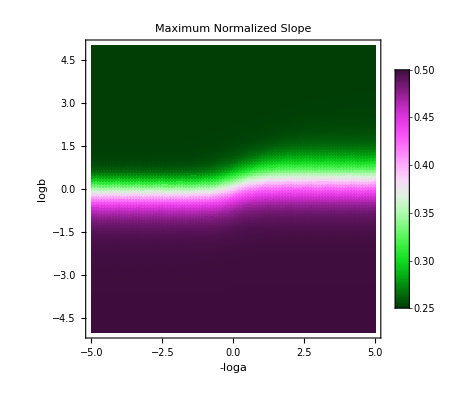

```mathematica
PlotMaxSlopeNegativea=Quiet[DensityPlot[{MaxSlope[-10^loga,10^logb]},{loga,logabounds[[1]][[1]],logabounds[[1]][[2]]},{logb,logbbounds[[1]][[1]],logbbounds[[1]][[2]]},PlotPoints->{Npoints[[1]],Npoints[[1]]},ColorFunction->"GreenPinkTones",FrameLabel->{"-loga","logb"},PlotLegends->Automatic,PlotLabel->"Maximum Normalized Slope",PlotRange->{Full,Full,Full}]]
```

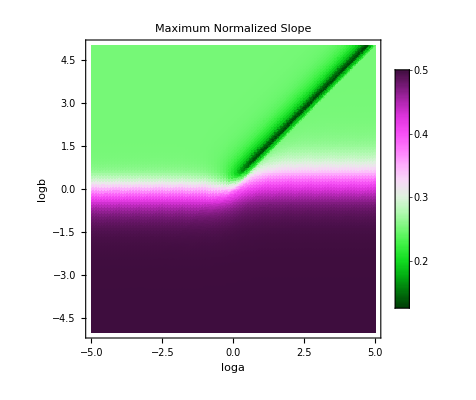

```mathematica
PlotMaxSlopePostivea=Quiet[DensityPlot[{MaxSlope[10^loga,10^logb]},{loga,logabounds[[1]][[1]],logabounds[[1]][[2]]},{logb,logbbounds[[1]][[1]],logbbounds[[1]][[2]]},PlotPoints->{Npoints[[1]],Npoints[[1]]},ColorFunction->"GreenPinkTones",FrameLabel->{"loga","logb"},PlotLegends->Automatic,PlotLabel->"Maximum Normalized Slope",PlotRange->{Full,Full,Full}]]
```

```mathematica
(********************* PLOTS OF MAXIMUM SLOPE PER CURVE SHAPE *********************)
```

```mathematica
MaxSlope1Inflection[loga_,logb_]:=
If[Inflection1[10^loga,10^logb],
	SlopeAtInflectionForSinglyInflectedCurves[10^loga,10^logb]]

MaxSlope2Inflections[loga_,logb_,apos_]:=
If [apos,
	If[Inflection2[10^loga,10^logb],
		Max[SlopeAtLastInflectionForDoublyInflectedCurves[10^loga,10^logb],SlopeAtFristInflectionForDoublyInflectedCurves[10^loga,10^logb]]],
Max[SlopeAtLastInflectionForDoublyInflectedCurves[-10^loga,10^logb],SlopeAtFristInflectionForDoublyInflectedCurves[-10^loga,10^logb]]]

MaxSlope3Inflections[loga_,logb_]:=If[Inflection3[10^loga,10^logb],Max[SlopeAtLastInflectionForTriplyInflectedCurves[10^loga,10^logb],SlopeAtFirstInflectionForTriplyInflectedCurves[10^loga,10^logb]]]
```

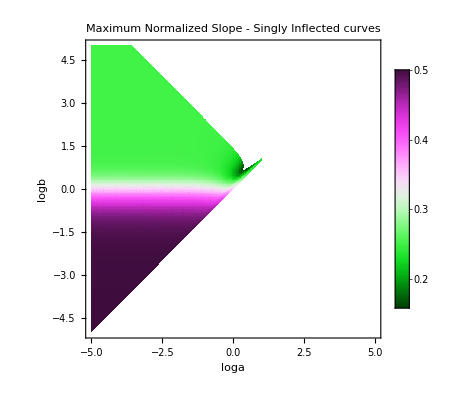

```mathematica
PlotMaxSlopeInflection1=Quiet[DensityPlot[{MaxSlope1Inflection[loga,logb]},{loga,logabounds[[1]][[1]],logabounds[[1]][[2]]},{logb,logbbounds[[1]][[1]],logbbounds[[1]][[2]]},PlotPoints->{Npoints[[2]],Npoints[[2]]},ColorFunction->"GreenPinkTones",FrameLabel->{"loga","logb"},PlotLegends->Automatic,PlotLabel->"Maximum Normalized Slope - Singly Inflected curves",PlotRange->{Full,Full,Full}]]
```

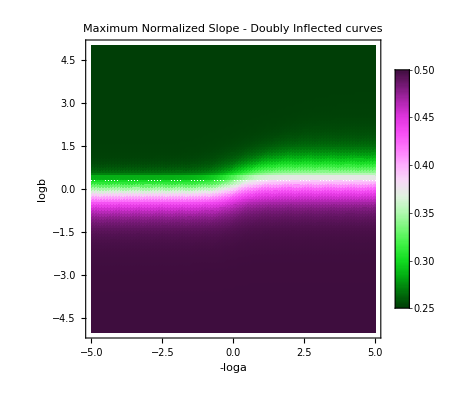

```mathematica
PlotMaxSlopeInflection2Negativea=Quiet[DensityPlot[{MaxSlope2Inflections[loga,logb,False]},{loga,logabounds[[1]][[1]],logabounds[[1]][[2]]},{logb,logbbounds[[1]][[1]],logbbounds[[1]][[2]]},PlotPoints->{Npoints[[1]],Npoints[[1]]},ColorFunction->"GreenPinkTones",FrameLabel->{"-loga","logb"},PlotLegends->Automatic,PlotLabel->"Maximum Normalized Slope - Doubly Inflected curves",PlotRange->{Full,Full,Full}]]
```

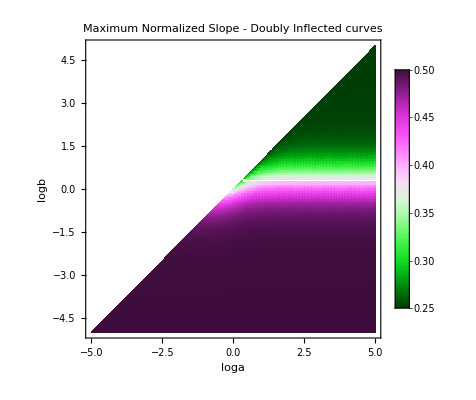

```mathematica
PlotMaxSlopeInflection2Positivea=Quiet[DensityPlot[{MaxSlope2Inflections[loga,logb,True]},{loga,logabounds[[1]][[1]],logabounds[[1]][[2]]},{logb,logbbounds[[1]][[1]],logbbounds[[1]][[2]]},PlotPoints->{Npoints[[1]],Npoints[[1]]},ColorFunction->"GreenPinkTones",FrameLabel->{"loga","logb"},PlotLegends->Automatic,PlotLabel->"Maximum Normalized Slope - Doubly Inflected curves",PlotRange->{Full,Full,Full}]]
```

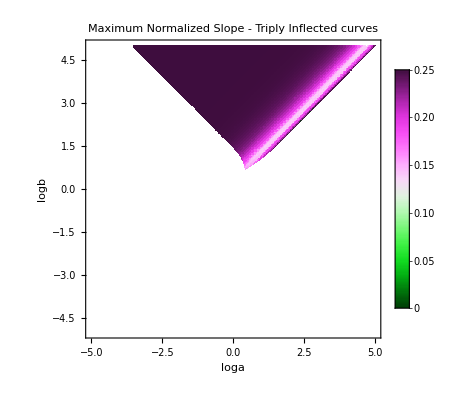

```mathematica
PlotMaxSlopeInflection3=Quiet[DensityPlot[{MaxSlope3Inflections[loga,logb]},{loga,logabounds[[1]][[1]],logabounds[[1]][[2]]},{logb,logbbounds[[1]][[1]],logbbounds[[1]][[2]]},PlotPoints->{Npoints[[1]],Npoints[[1]]},ColorFunction->"GreenPinkTones",FrameLabel->{"loga","logb"},PlotLegends->Automatic,PlotLabel->"Maximum Normalized Slope - Triply Inflected curves",PlotRange->{Full,Full,Full}]]
```

```mathematica
(********************* NUMERICAL BOUNDS ON MAXIMAL SLOPE PER CURVE SHAPE *********************)
```

```mathematica
MinMax1Inflection[list_]:=Module[{smin0=1,smax0=0,s,i},For[i=1,i<=Length[list],i++,s=N[MaxSlope1Inflection[list[[i,1]],list[[i,2]]]];
If[s>=smax0,smax0=s,If[s<=smin0,smin0=s]];];
{smin0,smax0}]

MinMax2Inflection[list_,apos_]:=Module[{smin0=1,smax0=0,s,i},For[i=1,i<=Length[list],i++,s=N[MaxSlope2Inflections[list[[i,1]],list[[i,2]],apos]];
If[s>=smax0,smax0=s,If[s<=smin0,smin0=s]];];
{smin0,smax0}]

MinMax3Inflection[list_]:=Module[{smin0=1,smax0=0,s,i},For[i=1,i<=Length[list],i++,s=N[MaxSlope3Inflections[list[[i,1]],list[[i,2]]]];
If[s>=smax0,smax0=s,If[s<=smin0,smin0=s]];];
{smin0,smax0}]
```

```mathematica
MinMax1Inflection[logabzoom]
MinMax2Inflection[logabzoom,True]
MinMax2Inflection[logabzoom,False]
MinMax3Inflection[logabzoom]
```

{0.159513,0.499997}

{0.250002,0.499999}

{0.25,0.499999}

{0.125297,0.25}

```mathematica
MinMax1Inflection[logab]
MinMax2Inflection[logab,True]
MinMax2Inflection[logab,False]
MinMax3Inflection[logab]
```

{0.167229,0.5}

{0.25,0.5}

{0.25,8.38861×10^6}

{0.125297,0.25}